```mathematica
data={{1790,3.93},{1800,5.31},{1810,7.24},{1820,9.64},{1830,12.87},{1840,17.07},{1850,23.19},{1860,31.44},{1870,39.83},{1880,50.16},{1890,62.95},{1900,75.99},{1910,91.97},{1920,105.71},{1930,122.78},{1940,131.67},{1950,151.33},{1960,179.32},{1970,203.21},{1980,226.50},{1990,248.71},{2000,281.42}};
```

```mathematica
data=MatrixForm[data];
```

```mathematica
data[[{1}]][[{1}]]
```

```mathematica
{{1790,3.93}}
```

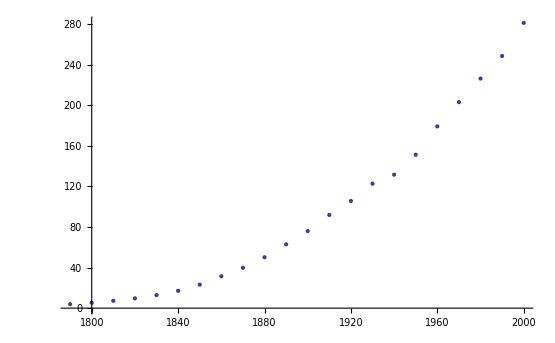

```mathematica
r = ListPlot[data]
```

```mathematica
data2 = Table[{data[[j,1]] -1790, data[[j,2]]}, {j,22}]
```

{{0,3.93},{10,5.31},{20,7.24},{30,9.64},{40,12.87},{50,17.07},{60,23.19},{70,31.44},{80,39.83},{90,50.16},{100,62.95},{110,75.99},{120,91.97},{130,105.71},{140,122.78},{150,131.67},{160,151.33},{170,179.32},{180,203.21},{190,226.5},{200,248.71},{210,281.42}}

```mathematica
p0 = ListPlot[data]
```

ListPlot::lpn: data is not a list of numbers or pairs of numbers.

ListPlot[data]

```mathematica
r = DSolve[{P'[t] == k P[t], P[0]  == 3.93}, P[t], t]
```

{{P[t]→3.93 ⅇ^(k t)}}

```mathematica
{{P[t]->ⅇ^(k t) C[1]}}
Clear[k]
```

{{P[t]→ⅇ^(k t) C[1]}}

```mathematica
r = DSolve[{P'[t] == c P[t], P[0] ==  3.93}, P[t], t]
```

```mathematica
{{P[t]->3.93 ⅇ^(c t)}}]
```

```mathematica
g[t_] = r[[1,1,2]]
```

3.93 ⅇ^(c t)

```mathematica
g[t_] = 3.93 ⅇ^(0.020339089473709236 t)
```

3.93 ⅇ^(0.0203391 t)

```mathematica
g[5]
```

```mathematica
3.93 ⅇ^(5 c)
Solve[{g[210] == 281.42}, c]
```

3.93 ⅇ^(5 c)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→0.0203391}}

```mathematica
p = Plot[g[m], {m, 0, 2000}, PlotStyle-> Red]
```

-Graphics-

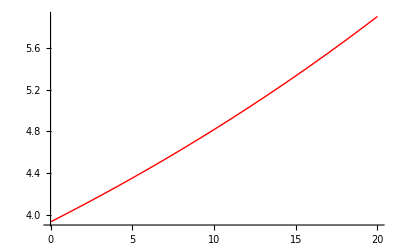

```mathematica
p2 = Plot[g[m], {m, 0, 20}, PlotStyle-> Red]
```

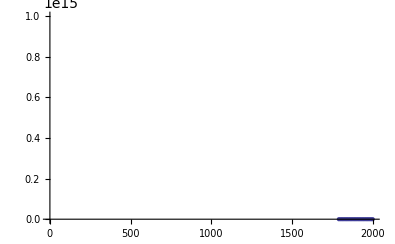

```mathematica
Show[p,r]
```